# Point Force Greens Functions

```mathematica
r = Sqrt[(x-xs)^2 +(y-ys)^2];
Upt =1/2/Pi*Log[r]
s12 = D[Upt,x]
s13 = D[Upt,y]
```

Log[√((x-xs)^2+(y-ys)^2)]/(2 π)

(x-xs)/(2 π ((x-xs)^2+(y-ys)^2))

(y-ys)/(2 π ((x-xs)^2+(y-ys)^2))

## Indefinite integration over a 2-dimensional domain

```mathematica
Uf = Integrate[Upt,xs,ys,GeneratedParameters->C]
```

1/(4 π)(x y+xs y-x ys-3 xs ys+2 (y-ys)^2 ArcTan[(x-xs)/(y-ys)]+(x^2-2 x xs+xs^2+y^2-y ys+ys^2) ArcTan[(y-ys)/(x-xs)]+y ys ArcTan[(-y+ys)/(x-xs)]+x y Log[(x-xs)^2+(y-ys)^2]-xs y Log[(x-xs)^2+(y-ys)^2]-x ys Log[(x-xs)^2+(y-ys)^2]+xs ys Log[(x-xs)^2+(y-ys)^2])+C[1][ys]+C[2][xs]

## Evaluate limits of integral

```mathematica
U2d =ReplaceAll[Uf,{xs->a,ys->b}]-ReplaceAll[Uf,{xs->a,ys->-b}]-ReplaceAll[Uf,{xs->-a,ys->b}]+ReplaceAll[Uf,{xs->-a,ys->-b}]//FullSimplify
```

1/(4 π)(-12 a b+2 (b-y)^2 ArcTan[(a-x)/(b-y)]+2 (b-y)^2 ArcTan[(a+x)/(b-y)]+(b^2+(a-x)^2-b y+y^2) ArcTan[(b-y)/(a-x)]-b y ArcTan[(b-y)/(a+x)]+(b^2+(a+x)^2-b y+y^2) ArcTan[(b-y)/(a+x)]+b y ArcTan[(-b+y)/(a-x)]+2 (b+y)^2 ArcTan[(a-x)/(b+y)]+2 (b+y)^2 ArcTan[(a+x)/(b+y)]+b y ArcTan[(b+y)/(a-x)]+(b^2+(a-x)^2+b y+y^2) ArcTan[(b+y)/(a-x)]+b y ArcTan[(b+y)/(a+x)]+(b^2+(a+x)^2+b y+y^2) ArcTan[(b+y)/(a+x)]+a b Log[(a-x)^2+(b-y)^2]-b x Log[(a-x)^2+(b-y)^2]-a y Log[(a-x)^2+(b-y)^2]+x y Log[(a-x)^2+(b-y)^2]+a b Log[(a+x)^2+(b-y)^2]+b x Log[(a+x)^2+(b-y)^2]-a y Log[(a+x)^2+(b-y)^2]-x y Log[(a+x)^2+(b-y)^2]+a b Log[(a-x)^2+(b+y)^2]-b x Log[(a-x)^2+(b+y)^2]+a y Log[(a-x)^2+(b+y)^2]-x y Log[(a-x)^2+(b+y)^2]+(a+x) (b+y) Log[(a+x)^2+(b+y)^2])

# Try to reduce ArcTan terms - deal with branch cuts

```mathematica
α = (4 a y (a^2+b^2-x^2-y^2))/(a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2);
β=(4 a y (a^2+b^2-x^2-y^2))/(a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2);
(α+β)/(1-α*β)//FullSimplify
```

(8 a y (a^2+b^2-x^2-y^2))/((a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2) (1-(16 a^2 y^2 (a^2+b^2-x^2-y^2)^2)/((a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2)^2)))

```mathematica
(b^2-b y+y^2) ArcTan[(b-y)/(a-x)]+(b^2-b y+y^2) ArcTan[(b-y)/(a+x)]+
(a-x)^2 ArcTan[(b-y)/(a-x)]+(a-x)^2 ArcTan[(b+y)/(a-x)]+
(a+x)^2 ArcTan[(b-y)/(a+x)]+(a+x)^2 ArcTan[(b+y)/(a+x)]+
(b^2+b y+y^2) ArcTan[(b+y)/(a-x)]+(b^2+b y+y^2) ArcTan[(b+y)/(a+x)]
```

(a-x)^2 ArcTan[(b-y)/(a-x)]+(b^2-b y+y^2) ArcTan[(b-y)/(a-x)]+(a+x)^2 ArcTan[(b-y)/(a+x)]+(b^2-b y+y^2) ArcTan[(b-y)/(a+x)]+(a-x)^2 ArcTan[(b+y)/(a-x)]+(b^2+b y+y^2) ArcTan[(b+y)/(a-x)]+(a+x)^2 ArcTan[(b+y)/(a+x)]+(b^2+b y+y^2) ArcTan[(b+y)/(a+x)]

```mathematica
2 (b-y)^2 ArcTan[-a^2+x^2+(b-y)^2,2a(b-y)]+
2 (b+y)^2 ArcTan[-(a^2-x^2-(b+y)^2),2 a (b+y)]+
(b^2+y^2)ArcTan[a^2-x^2-(b-y)^2,2 a (b-y)] +
(a-x)^2 ArcTan[-b^2+(a-x)^2+y^2,2 b (a-x)]+
(a+x)^2 ArcTan[-b^2+(a+x)^2+y^2,2 b (a+x)]+
(b^2+y^2) ArcTan[a^2-x^2-(b+y)^2,2 a (b+y)]+
b y ArcTan[(a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2) (1-(16 a^2 y^2 (a^2+b^2-x^2-y^2)^2)/((a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2)^2)),8 a y (a^2+b^2-x^2-y^2)]
```

(b^2+y^2) ArcTan[a^2-x^2-(b-y)^2,2 a (b-y)]+2 (b-y)^2 ArcTan[-a^2+x^2+(b-y)^2,2 a (b-y)]+(a-x)^2 ArcTan[-b^2+(a-x)^2+y^2,2 b (a-x)]+(a+x)^2 ArcTan[-b^2+(a+x)^2+y^2,2 b (a+x)]+(b^2+y^2) ArcTan[a^2-x^2-(b+y)^2,2 a (b+y)]+2 (b+y)^2 ArcTan[-a^2+x^2+(b+y)^2,2 a (b+y)]+b y ArcTan[(a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2) (1-(16 a^2 y^2 (a^2+b^2-x^2-y^2)^2)/((a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2)^2)),8 a y (a^2+b^2-x^2-y^2)]

```mathematica
U2dc = 1/(4 π)(-12 a b+
   (2 (b-y)^2 ArcTan[-a^2+x^2+(b-y)^2,2a(b-y)]+
b y ArcTan[a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2,4 a y (a^2+b^2-x^2-y^2)]+
2 (b+y)^2 ArcTan[-(a^2-x^2-(b+y)^2),2 a (b+y)]+
(b^2-b y+y^2)ArcTan[a^2-x^2-(b-y)^2,2 a (b-y)]+
(a-x)^2 ArcTan[-b^2+(a-x)^2+y^2,2 b (a-x)]+
(a+x)^2 ArcTan[-b^2+(a+x)^2+y^2,2 b (a+x)]+
(b^2+b y+y^2) ArcTan[a^2-x^2-(b+y)^2,2 a (b+y)])+
a b Log[(a-x)^2+(b-y)^2]-b x Log[(a-x)^2+(b-y)^2]-a y Log[(a-x)^2+(b-y)^2]+x y Log[(a-x)^2+(b-y)^2]+a b Log[(a+x)^2+(b-y)^2]+b x Log[(a+x)^2+(b-y)^2]-a y Log[(a+x)^2+(b-y)^2]-x y Log[(a+x)^2+(b-y)^2]+a b Log[(a-x)^2+(b+y)^2]-b x Log[(a-x)^2+(b+y)^2]+a y Log[(a-x)^2+(b+y)^2]-x y Log[(a-x)^2+(b+y)^2]+(a+x) (b+y) Log[(a+x)^2+(b+y)^2]);
U2dc = 1/(4 π)(-12 a b+
   (2 (b-y)^2 ArcTan[-a^2+x^2+(b-y)^2,2a(b-y)]+
2 (b+y)^2 ArcTan[-(a^2-x^2-(b+y)^2),2 a (b+y)]+
(b^2+y^2)ArcTan[a^2-x^2-(b-y)^2,2 a (b-y)] +
(a-x)^2 ArcTan[-b^2+(a-x)^2+y^2,2 b (a-x)]+
(a+x)^2 ArcTan[-b^2+(a+x)^2+y^2,2 b (a+x)]+
(b^2+y^2) ArcTan[a^2-x^2-(b+y)^2,2 a (b+y)]+
b y ArcTan[(a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2) (1-(16 a^2 y^2 (a^2+b^2-x^2-y^2)^2)/((a^4+b^4+2 b^2 (x-y) (x+y)+2 a^2 (b^2-x^2-3 y^2)+(x^2+y^2)^2)^2)),8 a y (a^2+b^2-x^2-y^2)])+
a b Log[(a-x)^2+(b-y)^2]-b x Log[(a-x)^2+(b-y)^2]-a y Log[(a-x)^2+(b-y)^2]+x y Log[(a-x)^2+(b-y)^2]+a b Log[(a+x)^2+(b-y)^2]+b x Log[(a+x)^2+(b-y)^2]-a y Log[(a+x)^2+(b-y)^2]-x y Log[(a+x)^2+(b-y)^2]+a b Log[(a-x)^2+(b+y)^2]-b x Log[(a-x)^2+(b+y)^2]+a y Log[(a-x)^2+(b+y)^2]-x y Log[(a-x)^2+(b+y)^2]+(a+x) (b+y) Log[(a+x)^2+(b+y)^2]);
```

# Plot displacement field

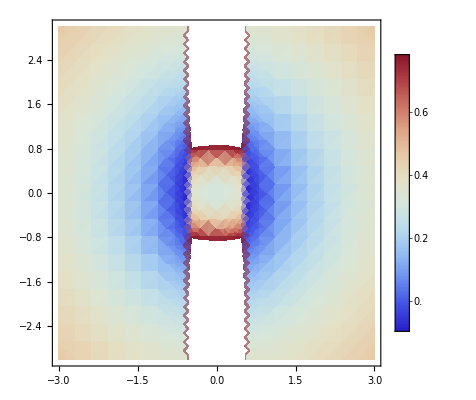

```mathematica
DensityPlot[ReplaceAll[U2d,{a->0.5,b->1}],{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->20]
```

1/(4 π)(2 ((-a+x) ArcTan[(b-y)/(a-x)]+(a+x) ArcTan[(b-y)/(a+x)]+(-a+x) ArcTan[(b+y)/(a-x)]+(a+x) ArcTan[(b+y)/(a+x)])+(-b+y) Log[(a-x)^2+(b-y)^2]+(b-y) Log[(a+x)^2+(b-y)^2]-(b+y) (Log[(a-x)^2+(b+y)^2]-Log[(a+x)^2+(b+y)^2]))

1/(4 π)(2 (2 (-b+y) ArcTan[(a-x)/(b-y)]+2 (-b+y) ArcTan[(a+x)/(b-y)]-b ArcTan[(b-y)/(a-x)]+y ArcTan[(b-y)/(a-x)]-b ArcTan[(b-y)/(a+x)]+y ArcTan[(b-y)/(a+x)]+2 b ArcTan[(a-x)/(b+y)]+2 y ArcTan[(a-x)/(b+y)]+2 b ArcTan[(a+x)/(b+y)]+2 y ArcTan[(a+x)/(b+y)]+b ArcTan[(b+y)/(a-x)]+y ArcTan[(b+y)/(a-x)]+(b+y) ArcTan[(b+y)/(a+x)])+(-a+x) Log[(a-x)^2+(b-y)^2]-(a+x) Log[(a+x)^2+(b-y)^2]+(a-x) Log[(a-x)^2+(b+y)^2]+(a+x) Log[(a+x)^2+(b+y)^2])

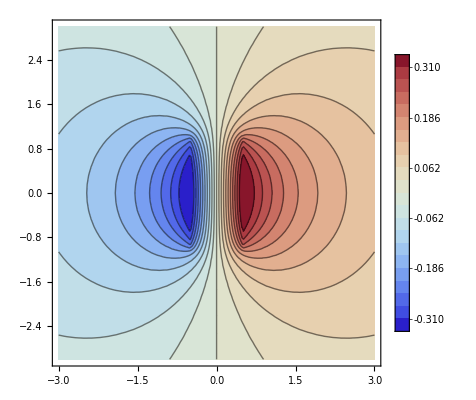

```mathematica
S12 = D[U2d,x]//FullSimplify
S13 = D[U2d,y]//FullSimplify
ContourPlot[ReplaceAll[S12,{a->0.5,b->1}],{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->Automatic,PlotPoints->20,Contours->21]
```

# Testing how to deal with ArcTan

The best way to deal with multiple ArcTan is to simplify the common terms using the following rules:


Following this, use the ArcTan[x,y] formula instead of ArcTan[y/x]

```mathematica
(*dummy = ArcTan[(y+1),x]-ArcTan[(y-1),x]//Simplify*)
(*dummy = ArcTan[x/(y+1)]-ArcTan[x/(y-1)]*)
(*dummy = ArcTan[(y+1),x]-ArcTan[(y-1),x]*)
(*dummy = ArcTan[1+x^2/(y^2-1),x/(y+1)-x/(y-1)]//FullSimplify*)
dummy = ArcTan[(x^2+y^2-1),-2x]
```

ArcTan[-1+x^2+y^2,-2 x]

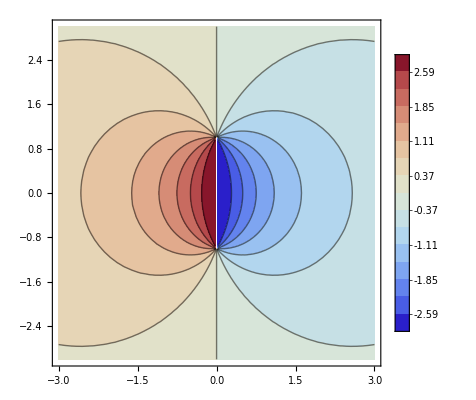

```mathematica
ContourPlot[dummy,{x,-3,3},{y,-3,3},ColorFunction->"ThermometerColors",PlotLegends->Automatic,Contours->15]
```